# Toy Model

## Introduction

------ Parameters ------

```mathematica
(* Model parameters *)
cg=15.;(*"Millimolar" -> glc in feed*)
Vg=0.5;(*"Millimoles"/"Grams"/"Hours" -> max glc uptake*)
R=0.4; (*"Millimoles"/"Grams"/"Hours" -> max uptake of pyruvate by mitochondria (max. respiration)*)
δlac=0.0022/2;(*1/"Millimolar"/"Hours" -> lac death rate*)
mE=1;(*"Millimoles"/"Grams"/"Hours" -> maintenance ATP demand*)
y=0.0040993788819875775;(* Units of atp needed to produce a unit of biomass *)
Nf = 2;(* stoichometric coeficient of fermentation *)
Nr = 19; (* stoichometric coeficient of respiration *)
ϕ = 1.(* Bleeding coefficient *);
Protect[cg,Vg,R,δlac,mE,y,Nf,Nr,ϕ];
```

------ Functions ------

### Balance equations and Constrains

Balance equation for P
Nf*vg + vl - vo = 0 →(6)

Balance equation  for ATP
Nf*vg + Nr*vo  = vapt  → (7)

Constraint of vg
vg ≤ min{Vg, cg * D/X}  → (8)

Constraint of vl
vl ≤ 0 → (9)

Contraint of vo
0 ≤ vo ≤ R → (9)

Taking the upper bound of vg you get Mg (The maximum glucose uptake)
Mg = min{Vg, cg *ξ}

### Growth function

Rate of biomass synthesis
We consider the ATP requirement of growth and maintinance and ingnore additional biomass components
z = (vatp - mE) * y 

Death rate
We assume that the secreted lactate is toxic, so the death will depend of its concentration in the culture (sl)
δ = δlac * sl 

Net growth rate
λ = z - δ 

Maximum net growth rate
The growth rate is maximum when vatp is maximum too
λmax = z[vatpmax] - δ → (0.5)

## Model Solution

------ Polytope (𝒫_s)------

### Definition

"The constraints and balance equations defined above define a polytope of feasible metabilic states that we denote (𝒫_s). Each point within this space, in the Toy model, consists of coordinates v = (vg,vatp), wich fully specify the metabolic state of a cell in the model. "

### Polytope limits

" To do any calculation through the polytope it is useful to defind its limits... "

```mathematica
vgMinGlobal = 0;
vgMaxGlobal[ξ_] := Min[Vg,cg/ξ];
vgMinLocal[vatp_]:=Max[vatp/(1+Nr),vatp-Nr*R]/Nf;
vgMaxLocal[ξ_][vatp_]:=Min[vgMaxGlobal[ξ],vatp/Nf];

vatpMinGlobal = vatpMinLocal[vgMinGlobal];
vatpMaxGlobal[ξ_]:=vatpMaxLocal[vgMaxGlobal[ξ]];
vatpMinLocal [vg_] := Nf*vg; 
vatpMaxLocal[vg_] := Min[Nf(1+Nr)vg,Nf*vg+Nr*R];

SetAttributes[{vatpMaxGlobal,vatpMaxLocal,vatpMinGlobal,vatpMinLocal,vgMaxGlobal,vgMaxLocal,vgMinGlobal,vgMinLocal},{NumericFunction, Protected}];
```

"All points in the polytope most solve the constraints 0 ≤ vg ≤ Mg  &&  vl ≤ 0 && 0 ≤ vo ≤ R, with littler transformations this constrains are turned into vgMinLocal ≤ vg ≤ vgMaxLocal && vatpMinLocal ≤ vatp ≤ vatpMaxLocal"

```mathematica
polytope[ξ_][vatp_,vg_]:=vgMinLocal[vatp]≤vg≤vgMaxLocal[ξ][vatp] && vatpMinLocal[vg] ≤ vatp ≤ vatpMaxLocal[vg]; SetAttributes[polytope,Protected];
```

```mathematica
showPolytopeξdependencyTest
```

------ Probability Distribution------

### Maximum Entropy and Probabolity Distribution

" Let P(v) be the probabilistic density of cells with metabolic fluxes v. To determine the form of P(v)dv, we adopt the Princile of Maximum Entropy (MaxEnt), which in this context can be  stated as follows:"

" Given the set of allowed metabolic states (𝒫_s), the dependency of the cellular growth rate with metabolic fluxes (λ_s(v)), and the average growth rate of the cell population ⟨λ⟩, the distribution of cells within 𝒫_s has the form ⅇ^(β*λ[v]),"

```mathematica
zDistribution[ξ_,β_,vatp_] := Exp[-β y(vatpMaxGlobal[ξ]-vatp)];
SetAttributes[zDistribution, {NumericFunction,Protected}]
```

"where β is chosen so that the expectation of λ under (𝒫_s) coincides with ⟨λ⟩."

```mathematica
showZDistributionβdependencyTest
```

### Normalized Distribution

"So, the normalized distribution can be defined"

```mathematica
normalizedDistribution[ξ_,β_,vatp_,totalIntegral_] := distributionOfCells[ξ,β,vatp]/totalIntegral;
```

" where totalIntegral is the value of the integral in the whole polytope, "

```mathematica
totalIntegral[ξ_,β_] := ∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) distributionOfCells[ξ,β,vatp]ⅆvg)ⅆvatp ;
```

Normalized Probability Density Function

ξ value: 2

Total Integral Test -> {1.,1.,1.}

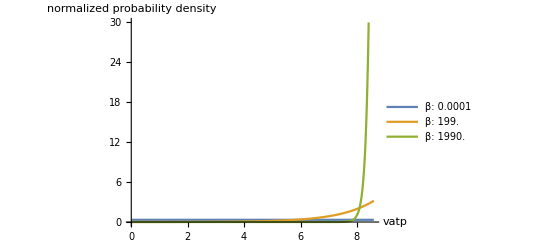

```mathematica
showNormalizedDistribution[2]
```

### Probability associated to vatp

" So, the probability of vatp in the population of cells can be calculated: “

```mathematica
vatpDistribution[ξ_,β_,vatp_,totalIntegral_] := ∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) normalizedDistribution[ξ,β,vatp,totalIntegral]ⅆvg;
```

Propbability Density of Vatp

ξ value: 2

Total Integral Test -> {1.,1.,1.}

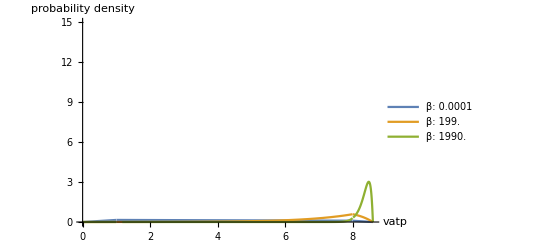

```mathematica
showVatpDistribution[2]
```

### Probability associated to vg

" Also, the probability of vg is calculated as: “

```mathematica
vgDistribution[ξ_,β_,vg_,totalIntegral_] := ∫_vatpMinLocal[vg]^vatpMaxLocal[vg] normalizedDistribution[ξ,β,vatp,totalIntegral]ⅆvatp;
```

Propbability Density of Vg

Total Integral Test -> {1.,1.,1.}

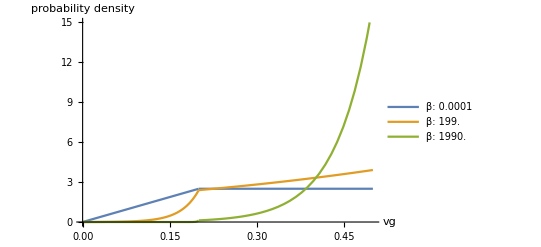

```mathematica
showVgDistribution[2]
```

## Results

"In this toy model, the total consumption of glucose of the population of cells can be estimated“

```mathematica
expectedVg[ξ_,β_] := ∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) normalizedDistribution[ξ,β,vatp, totalIntegral[ξ,β]]vgⅆvg)ⅆvatp;
```

"Next, the value of the glucose concentration are obtained from...“

```mathematica
s[ξ_,β_] :=Max[0, cg - expectedVg[ξ,β]ξ];
```

"The expected waste uptake are given by..."

Substrate Concentration

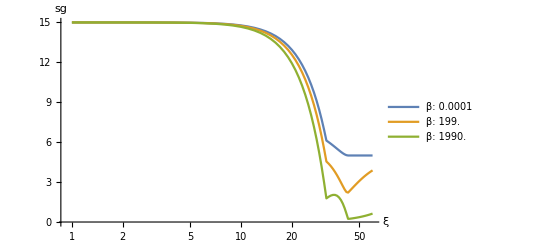

```mathematica
showSubstrateConcentration
```

```mathematica
expectedVw[ξ_,β_] := ∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) normalizedDistribution[ξ,β,vatp, totalIntegral[ξ,β]]((vatp -38 expectedVg[ξ,β])/18)ⅆvg)ⅆvatp//N;
```

"The same way, we can calculated the waste concentration in the medium...“

```mathematica
w[ξ_,β_] :=Max[0, - expectedVw[ξ,β]*ξ];
```

Waste Concentration

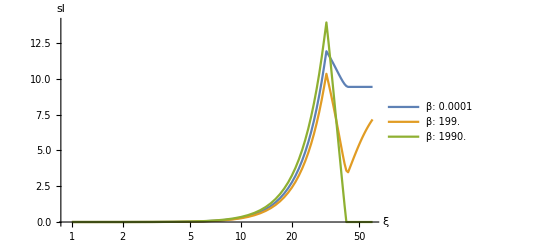

```mathematica
showWasteConcentration
```

```mathematica
expectedZ[ξ_, β_] := ∫_vatpMinGlobal^vatpMaxGlobal[ξ] (∫_vgMinLocal[vatp]^(vgMaxLocal[ξ][vatp]) ((vatp - mE)*y)ⅆvg)ⅆvatp//N;
λ[ξ_,β_] := expectedZ[ξ,β] - δlac * w[ξ,β]; 
d[ξ_,β_] := λ[ξ,β]/ϕ;
```

Dilution Rate

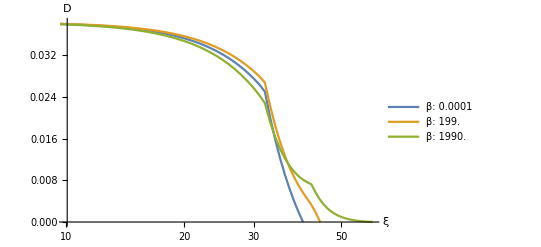

```mathematica
showDilutionRate
```

```mathematica
x[ξ_,β_] := λ[ξ,β]*ξ/ϕ;
```

Cell Density

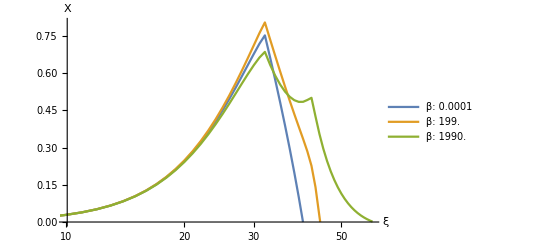

```mathematica
showCellDensity
```

```mathematica
Table[ξ/ 0.04629629629629629,{ξ, {1.299277474965141,5.817363694176957,15.289083670430593,27.77777777777777}}]
```

{28.0644,125.655,330.244,600.}

## Graphic Functions

```mathematica
(* Graphic funtions *)
Module[{vatpAxeRange,vatpAxeLabel,vgAxeRange,vgAxeLabel,ξAxeRange,ξAxeLabel,ξunit, ξlist,βlist,ξmax},
(* General parameters *)
ξmax = {1.299277474965141,5.817363694176957,15.289083670430593,27.77777777777777}; (* The max values of ξ to test each βlist values *)
ξunit = 0.04629629629629629;(* A convertion factor of ξ *)
βlist  = {0,199.,1990.,∞}; (* Values of β to be test *)
ξlist = {1, 50.,100.,500,1000,5000} ;
vgAxeRange = {vgMinGlobal - vgMaxGlobal[Last[ξmax]]*0.1, vgMaxGlobal[Last[ξmax]]*1.1};
vgAxeLabel = "v_glc (mmol/h/gDW)";
vatpAxeLabel = "v_atp (mmol/h/gDW)";
vatpAxeRange= {vatpMinGlobal - vatpMaxGlobal[Last[ξmax]]*0.1, vatpMaxGlobal[Last[ξmax]]*1.1};
ξAxeRange = {0,Last[ξmax]};
ξAxeLabel = "ξ (10^6 cells·day/mL)";

ClearAll[plotPolytope];
plotPolytope[ξ_] := RegionPlot[polytope[ξ][vatp,vg],
{vatp, vatpMinGlobal , vatpMaxGlobal[ξ] },
{vg, vgMinGlobal , vgMaxGlobal[ξ]},
FrameLabel->{vatpAxeLabel,vgAxeLabel},
 AspectRatio-> 0.7, 
PlotRange-> {vatpAxeRange, vgAxeRange}];

ClearAll[showPolytopeξdependencyTest];
showPolytopeξdependencyTest := Manipulate[Show[plotPolytope[ξ]],{ξ,0.001,1000}];

ClearAll[plotZDensity];
plotZDensity[ξ_,β_] := DensityPlot[zDistribution[ξ,β,vatp],{vatp, vatpMinGlobal , vatpMaxGlobal[ξ] },
{vg, vgMinGlobal , vgMaxGlobal[ξ]},
RegionFunction-> Function[{vatp,vg} , polytope[ξ][vatp,vg]], 
FrameLabel->{vatpAxeLabel,vgAxeLabel},
AspectRatio-> 0.7, 
PlotRange-> Full,
BoundaryStyle->Black
];

ClearAll[showZDistributionβdependencyTest];
showZDistributionβdependencyTest := Manipulate[Show[plotPolytope[ξ],plotZDensity[ξ,β]],{ξ,0.001,1000},{β,0.001,3000}];


];
showZDistributionβdependencyTest
```

```mathematica
ClearAll[ξlist];
ξlist = {1, 50.,100.,500,1000,5000} ;
ξlist[[FirstPosition[ξlist, 100.]]]
```

{100.}